## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
Get[dddRicardo]
```

```mathematica
Data = <|"Vertices List"->{1,2,3,4},"Adjacency Matrix"->{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1},{4,U2}},"Switching Costs"->{{1,2,3,S1},{1,2,4,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>;
```

```mathematica
d2e=Data2Equations[Data/.{I1->1,U1->0,U2->1, 
S1->3,S2->0,S3->0,S4->0,S5->3,S6->3}];
(crit=CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

Iterative boolean convert took 0.006836 seconds to terminate

Iterative boolean convert took 0.002261 seconds to terminate

Iterative boolean convert took 0.002202 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {-1≤u3≤0,<|j12→1,j11→0,j7→0,j9→0,j2→1,j1→0,j4→0,j6→1,j3→0,j8→0,j5→0,j10→1,u8→0,u10→1,jt10→0,jt11→1,jt12→0,jt2→1,jt4→1,jt5→0,jt6→0,jt8→0,jt9→0,u12→3,u7→0,u9→1,jt1→0,jt7→0,u11→3,u2→2,u4→u3,u6→1,jt3→0,u1→3,u5→2|>}

Picked one value for the variable(s) {u3}

{0.025596,Null}

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

EqEntryIn: True
j12==1

EqValueAuxiliaryEdges: True
u11==u12&&u7==u8&&u9==u10

EqCompCon: True
(jt1==0||1000000-u1+u12==0)&&(jt2==0||u1-u12==0)&&(jt3==0||3-u2+u3==0)&&(jt4==0||-u2+u5==0)&&(jt5==0||u2-u3==0)&&(jt6==0||-u3+u5==0)&&(jt7==0||3+u2-u5==0)&&(jt8==0||3+u3-u5==0)&&(jt9==0||-u4+u7==0)&&(jt10==0||1000000+u4-u7==0)&&(jt11==0||-u6+u9==0)&&(jt12==0||1000000+u6-u9==0)

EqBalanceSplittingCurrents: True
j1==jt1&&j12==jt2&&j2==jt3+jt4&&j3==jt5+jt6&&j5==jt7+jt8&&j4==jt9&&j7==jt10&&j6==jt11&&j9==jt12

EqCurrentCompCon: True
(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)

EqTransitionCompCon: True
(jt1==0||jt2==0)&&(jt10==0||jt9==0)&&(jt11==0||jt12==0)&&(jt3==0||jt5==0)&&(jt4==0||jt7==0)&&(jt6==0||jt8==0)

EqPosJs: True
j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0

EqPosJts: True
jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0

EqSwitchingByVertex: True
u1≤1000000+u12&&u12≤u1&&u2≤3+u3&&u2≤u5&&u3≤u2&&u3≤u5&&u5≤3+u2&&u5≤3+u3&&u4≤u7&&u7≤1000000+u4&&u6≤u9&&u9≤1000000+u6

Nlhs: {0,0,0}
{-1. j1+j2-1. u1+u2,-1. j3+j4-1. u3+u4,-1. j5+j6-1. u5+u6}

Nrhs: {0.0741253,0.,0.0741253}
{-j1+j2-IntM[-j1+j2,1->2],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,2->4]}

Max error for non-linear solution: 0.0741253

<|j12→1,j11→0,j7→0,j9→0,j2→1,j1→0,j4→0,j6→1,j3→0,j8→0,j5→0,j10→1,u8→0,u10→1,jt10→0,jt11→1,jt12→0,jt2→1,jt4→1,jt5→0,jt6→0,jt8→0,jt9→0,u12→3,u7→0,u9→1,jt1→0,jt7→0,u11→3,u2→2,u4→-25/34,u6→1,jt3→0,u1→3,u5→2,u3→-25/34|>

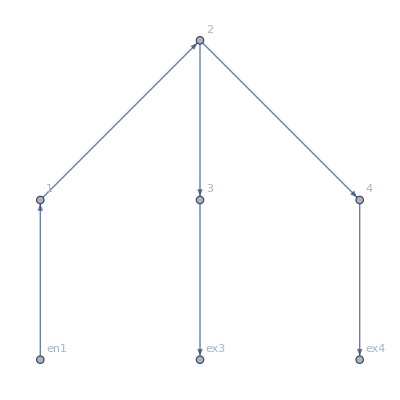

```mathematica
crit["FG"]
crit["uvars"]/.crit["AssoCritical"]
```

```mathematica
nn=NonLinear[crit];
IsNonLinearSolution[nn]@nn["AssoNonCritical"]
```

Iterative boolean convert took 0.006269 seconds to terminate

Iterative boolean convert took 0.002009 seconds to terminate

Iterative boolean convert took 0.001949 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {-268531321928177/250000000000000≤u3≤0,<|j12→1,j11→0,j7→0,j9→0,j2→1,j1→0,j4→0,j6→1,j3→0,j8→0,j5→0,j10→1,u8→0,u10→1,jt10→0,jt11→1,jt12→0,jt2→1,jt4→1,jt5→0,jt6→0,jt8→0,jt9→0,u12→356468678071823/125000000000000,u7→0,u9→1,jt1→0,jt7→0,u11→356468678071823/125000000000000,u2→481468678071823/250000000000000,u4→u3,u6→1,jt3→0,u1→356468678071823/125000000000000,u5→481468678071823/250000000000000|>}

Picked one value for the variable(s) {u3}

Iterative boolean convert took 0.005787 seconds to terminate

Iterative boolean convert took 0.002102 seconds to terminate

Iterative boolean convert took 0.002017 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {-268531321928177/250000000000000≤u3≤0,<|j12→1,j11→0,j7→0,j9→0,j2→1,j1→0,j4→0,j6→1,j3→0,j8→0,j5→0,j10→1,u8→0,u10→1,jt10→0,jt11→1,jt12→0,jt2→1,jt4→1,jt5→0,jt6→0,jt8→0,jt9→0,u12→356468678071823/125000000000000,u7→0,u9→1,jt1→0,jt7→0,u11→356468678071823/125000000000000,u2→481468678071823/250000000000000,u4→u3,u6→1,jt3→0,u1→356468678071823/125000000000000,u5→481468678071823/250000000000000|>}

Picked one value for the variable(s) {u3}

Iterated 2 times out of 15

EqEntryIn: j12==1	True

EqValueAuxiliaryEdges: u11==u12&&u7==u8&&u9==u10	True

EqCompCon: (jt1==0||1000000-u1+u12==0)&&(jt2==0||u1-u12==0)&&(jt3==0||3-u2+u3==0)&&(jt4==0||-u2+u5==0)&&(jt5==0||u2-u3==0)&&(jt6==0||-u3+u5==0)&&(jt7==0||3+u2-u5==0)&&(jt8==0||3+u3-u5==0)&&(jt9==0||-u4+u7==0)&&(jt10==0||1000000+u4-u7==0)&&(jt11==0||-u6+u9==0)&&(jt12==0||1000000+u6-u9==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j12==jt2&&j2==jt3+jt4&&j3==jt5+jt6&&j5==jt7+jt8&&j4==jt9&&j7==jt10&&j6==jt11&&j9==jt12	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt9==0)&&(jt11==0||jt12==0)&&(jt3==0||jt5==0)&&(jt4==0||jt7==0)&&(jt6==0||jt8==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0	True

EqSwitchingByVertex: u1≤1000000+u12&&u12≤u1&&u2≤3+u3&&u2≤u5&&u3≤u2&&u3≤u5&&u5≤3+u2&&u5≤3+u3&&u4≤u7&&u7≤1000000+u4&&u6≤u9&&u9≤1000000+u6	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}	{0.0741253,0.,0.0741253}

Nrhs: {-j1+j2-IntM[-j1+j2,1->2],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,2->4]}	{0.0741253,0.,0.0741253}

Max error for non-linear solution: 4.30211×10^-16

<|j12→1,j11→0,j7→0,j9→0,j2→1,j1→0,j4→0,j6→1,j3→0,j8→0,j5→0,j10→1,u8→0,u10→1,jt10→0,jt11→1,jt12→0,jt2→1,jt4→1,jt5→0,jt6→0,jt8→0,jt9→0,u12→356468678071823/125000000000000,u7→0,u9→1,jt1→0,jt7→0,u11→356468678071823/125000000000000,u2→481468678071823/250000000000000,u4→-4/5,u6→1,jt3→0,u1→356468678071823/125000000000000,u5→481468678071823/250000000000000,u3→-4/5|>